# PLANO DE FOGO PARA TÚNEIS PILÃO DE QUATRO SEÇÕES

Resolver;

```mathematica
Remove["Global`*"]
```

# ARREDONDAMENTO

```mathematica
Arr[x_,n_]:=If[FractionalPart[x*10^n]<0.5,N[IntegerPart[x*10^n]/10^n],N[(IntegerPart[x*10^n]+1)/10^n]]
```

## DADOS DE ENTRADA

```mathematica
L=6;(*Largura do túnel em m*)
Hp=6;(*Altura das paredes do túnel em m*)
Harc=0.8;(*Altura do arco em m*)
ϕ=0.102;(*Diâmetro do furo vazio em m*)
d=0.038;(*Diâmetro dos furos em m*)
c=0.4;(*Constante da rocha*)
Explosivo =Emulite150; (*Tipo do explosivo*)
ϕExp={0.025,0.030,0.04};(*Diâmetro dos Cartuchos de explosivos em m*)
LExp=0.6; (*Comprimento dos cartuchos em m*)
```

## RELAÇÃO DE FORÇA DO EXPLOSIVO RELATIVA AO ANFO

```mathematica
Qvo=5;(*Calor Liberado na decomposição de 1kg de Dinamite-LFB*)
Vgaso=0.85;(*Volume de Gás Liberado na decomposição de 1kg de Dinamite-LFB*)
SLFBanfo=0.84; (*Força relativa do explosivo em relação ao ANFO*)
If[Explosivo == LFBDynamite, {Qv = 5,Vgas = 0.850, dExp = 1450}];
If[Explosivo == DynamexM, {Qv = 4.7,Vgas = 0.88, dExp = 1400}];
If[Explosivo == ANFO, {Qv = 3.91,Vgas = 0.973, dExp = 900}];
If[Explosivo == TNT, {Qv = 5.1,Vgas = 0.610, dExp = 1640}];
If[Explosivo == PETN, {Qv = 6,38,Vgas = 0.973, dExp =1670}];
If[Explosivo == Nabit, {Qv = 4,42,Vgas = 0.904, dExp = 1200}];
If[Explosivo == GuritA, {Qv = 3.8,Vgas = 0.4, dExp = 1000}];
If[Explosivo == NG, {Qv = 6.27,Vgas = 0.716, dExp = 1590}];If[Explosivo == Emulite150, {Qv = 4.1,Vgas = 0.84, dExp = 1200}];If[Explosivo == Iremite62, {Qv = 3.75,Vgas = 0.852, dExp = 1180}];If[Explosivo == IregelRX, {Qv = 2.68,Vgas = 0.941, dExp = 1200}];If[Explosivo == Dynex205, {Qv = 4,Vgas = 0.863, dExp = 1170}];If[Explosivo == Powergel2131, {Qv = 3.29,Vgas = 0.81, dExp = 1150}];
If[Explosivo == Kimit80, {Qv = 4.1,Vgas = 0.74, dExp = 1100}];
If[Explosivo == Emulet20, {Qv = 2.4,Vgas = 1.12, dExp = 220}];

SLFB=(5Qv)/(6Qvo)+Vgas/(6Vgaso);(*Relação de força do explosivo em relação à Dinamite-LFB*)
Sanfo=SLFB/SLFBanfo;(*Relação de força do explosivo em relação ao ANFO*)
```

## CONCENTRAÇÃO LINEAR DE CARGA

```mathematica
lExp=π(ϕExp/2)^2 dExp;(*Concentração linear de carga dos cartuchos*)
```

## AVANÇO

```mathematica
H=0.15+34.1ϕ-39.3 ϕ^2;(*Profundidade da perfuração*)
```

```mathematica
Ia=0.95H;(*Avanço do desmonte*)
```

## PILÃO - PRIMEIRO QUADRILÁTERO

```mathematica
B1=1.5ϕ;(*Encargo recomendável para desvios menores que 1%*)
```

```mathematica
l1=55d(B1/ϕ)^1.5(B1-ϕ/2)(c/0.4)(1/Sanfo);(*Concentração linear de carga requerida*)
```

```mathematica
deltal1 = lExp-l1 ;(*Seleção da carga mais próxima*)
l1 = l1 + Min[deltal1];
```

```mathematica
ht=10d;(*Comprimento do tampão*)
```

```mathematica
A1=√2 B1;(*Distância entre furos*)
```

```mathematica
NCexp1q=(H-ht)/LExp;(*Número de cartuchos de explosivos*)
NCexp1q = Arr[NCexp1q,1];
```

```mathematica
lfuro1q=NCexp1q LExp l1;(*Carga de explosivo por furo*)
```

```mathematica
lTotal1q=4lfuro1q;(*Carga total*)
```

## PILÃO - SEGUNDO QUADRILÁTERO

```mathematica
B2=0.088 √((A1 lExp Sanfo)/(d c));(*Encargo máximo*)
```

```mathematica
Bx2 = Select[B2, # ≤ (2*A1) &]; (*Seleção de B2 de acordo com as restrições*)
B2 = Max[Bx2] ;(*Escolha do maior encargo que atende às restrições*)
```

```mathematica
l2= ((B2/0.088)^2)*((d c)/(A1 Sanfo));(*Concentração linear de carga selecionada*)
```

```mathematica
ht=10d;(*Comprimento do tampão*)
```

```mathematica
A2=√2(B2+A1/2);(*Distância entre furos*)
```

```mathematica
NCexp2q=(H-ht)/LExp;(*Número de cartuchos de explosivos*)
NCexp2q = Arr[NCexp2q,1];
```

```mathematica
lfuro2q=NCexp2q LExp l2;(*Carga de explosivo por furo*)
```

```mathematica
lTotal2q=4lfuro2q;(*Carga total*)
```

## PILÃO - TERCEIRO QUADRILÁTERO

```mathematica
B3=0.088 √((A2 lExp Sanfo)/(d c));(*Encargo máximo*)
Bx3 = Select[B3, # ≤ (2*A2) &]; (*Seleção de B3 de acordo com as restrições*)
B3 = Max[Bx3]; (*Escolha do maior encargo que atende às restrições*)
```

```mathematica
l3= ((B3/0.088)^2)*((d c)/(A2 Sanfo));(*Concentração linear de carga selecionada*)
```

```mathematica
ht=10d;(*Comprimento do tampão*)
```

```mathematica
A3=√2(B3+A2/2);(*Distância entre furos*)
```

```mathematica
NCexp3q=(H-ht)/LExp;(*Número de cartuchos de explosivos*)
NCexp3q = Arr[NCexp3q,1];
```

```mathematica
lfuro3q=NCexp3q LExp l3;(*Carga de explosivo por furo*)
```

```mathematica
lTotal3q=4lfuro3q;(*Carga total*)
```

## PILÃO - QUARTO QUADRILÁTERO

```mathematica
B4=0.088 √((A3 lExp Sanfo)/(d c));(*Encargo máximo*)
Bx4 = Select[B4, # ≤ (2*A3) &]; (*Seleção de B3 de acordo com as restrições*)
B4 = Max[Bx4]; (*Escolha do maior encargo que atende às restrições*)
```

```mathematica
l4= ((B4/0.088)^2)*((d c)/(A3 Sanfo));(*Concentração linear de carga selecionada*)
```

```mathematica
ht=10d;(*Comprimento do tampão*)
```

```mathematica
A4=√2(B4+A3/2);(*Distância entre furos*)
```

```mathematica
NCexp4q=(H-ht)/LExp;(*Número de cartuchos de explosivos*)
NCexp4q = Arr[NCexp4q,1];
```

```mathematica
lfuro4q=NCexp4q LExp l4 ;(*Carga de explosivo por furo*)
```

```mathematica
lTotal4q=4lfuro4q;(*Carga total*)
```

## FUROS DE LEVANTE

```mathematica
lL=Max[lExp];(*Maior concentração linear de carga disponível*)
f = 1.45; (*Fator de fixação*)
BL=0.9 √((lL Sanfo)/(c f));(*Encargo dos furos de levante*)
```

```mathematica
ccor=If[BL≥ 1.4,c+0.05,c+0.07/BL];(*B≥1.4:c+0.05, B<1.4:c+0.07/B - Constante da rocha corrigida*)
```

```mathematica
BL=0.9 √((lL Sanfo)/(ccor f));(*Encargo dos furos de levante corrigido*)
```

```mathematica
NfL=IntegerPart[L/BL+2];(*Número de furos de levante*)
```

```mathematica
SL=L/(NfL-1);(*Espaçamento dos furos de levante*)
```

```mathematica
hcfL=1.25BL;(*Comprimento da carga de fundo*)
hccL=H-hcfL-10 d;(*Comprimento da carga de coluna*)
```

```mathematica
NCexpcfL=hcfL/LExp;(*Número de cartuchos de explosivos na carga de fundo*)
NCexpcfL = Arr[NCexpcfL,1];
```

```mathematica
NCexpccL=hccL/LExp;(*Número de cartuchos de explosivos na carga de coluna*)
NCexpccL = Arr[NCexpccL,1];
```

```mathematica
lLcc = Extract[lExp,{2}] ;(* Seleciona o explosivo com concentração de carga intermediária*)
```

```mathematica
lfuroL=(NCexpcfL LExp lL) + (NCexpccL LExp lLcc);(*Carga de explosivo por furo*)
```

```mathematica
lTotalL=NfL lfuroL;(*Carga total*)
```

## FUROS DE CONTORNO DO TETO

```mathematica
SCT=15d; (*Espaçamento dos furos de contorno no teto com k=15*)
```

```mathematica
BCT=0.8SCT;(*Encargo dos furos de contorno no teto*)
```

```mathematica
lCT=90 d^2;(*Concentração linear de carga recomendada*)
```

```mathematica
lCT=Min[lExp];(*Menor concentração linear de carga disponível*)
```

```mathematica
Carc[L_,Harc_]:=((4 Harc^2+L^2) ArcSin[(4 Harc L)/(4 Harc^2+L^2)])/(4 Harc);(*Comprimento do arco dados a largura
da seção L e a altura do arco Harc*)
Carco=Carc[L,Harc];(*Comprimento do arco do teto*)
```

```mathematica
NfCT=IntegerPart[Carco/SCT+2];(*Número de furos de contorno no teto*)
```

```mathematica
SCT = Carco/(NfCT -1) ;(*Espaçamento dos furos de contorno no teto ajustado*)
```

```mathematica
NCexpCT=H/LExp;(*Número de cartuchos de explosivos*)
NCexpCT = Arr[NCexpCT,1];
```

```mathematica
lfuroCT=NCexpCT LExp lCT; (*Carga de explosivo por furo*)
```

```mathematica
lTotalCT=NfCT lfuroCT ;(*Carga total*)
```

## FUROS DE CONTORNO DAS PAREDES

```mathematica
HrCP=Hp-SCT-BL;(*Altura remanescente da parede para os furos de contorno*)
```

```mathematica
lCP=Extract[lExp,{1}];(*Concentração linear de carga mínima*)
f=1.2;(*Fator de fixação*)
SB=1.25;(*Relação espaçamento/encargo*)
BCP=0.9 √((lCP Sanfo)/(c f SB));(*Encargo dos furos de contorno das paredes*)
ccor=If[BCP≥ 1.4,c+0.05,c+0.07/BCP];
BCP=0.9 √((lCP Sanfo)/(ccor f SB));(*Encargo corrigido dos furos de contorno da parede*)
```

```mathematica
NfCP=IntegerPart[HrCP/(BCP SB)+2];(*Número de furos de contorno por parede*)
NfCPT = 2 NfCP; (*Número total de furos da parede*)
```

```mathematica
SCP=HrCP/(NfCP-1);(*Espaçamento dos furos de contorno das paredes*)
```

```mathematica
hcfCP=1.25BCP;(*Comprimento da carga de fundo*)
hccCP=H-hcfCP-10 d;(*Comprimento da carga de coluna*)
```

```mathematica
NCexpcfCP=hcfCP/LExp;(*Número de cartuchos de explosivos na carga de fundo*)
NCexpcfCP = Arr[NCexpcfCP,1];
```

```mathematica
NCexpccCP=hccCP/LExp;(*Número de cartuchos de explosivos na carga de coluna*)
NCexpccCP = Arr[NCexpccCP,1];
```

```mathematica
lCPcc = Extract[lExp,{2}]; (* Seleciona o explosivo com concentração de carga intermediária*)
```

```mathematica
lfuroCP=(NCexpcfCP LExp lCP) + (NCexpccCP LExp lCPcc); (*Carga de explosivo por furo*)
```

```mathematica
lTotalCP=NfCPT lfuroCP;(*Carga total*)
```

## FUROS DE EXPANSÃO LATERAIS

```mathematica
LrEL=L-A4-2BCP;(*Largura remanescente para os furos laterais*)
```

```mathematica
f=1.45;(*Fator de fixação*)
SB=1.25;(*Relação espaçamento/encargo*)
BEL=0.9 √((lExp Sanfo)/(c f SB));(*Encargo dos furos de expansão laterais*)
DeltaBEL = LrEL - BEL;
DeltaBEL = Select[DeltaBEL, # > 0 &];
DeltaBEL = Max[DeltaBEL];
BEL = LrEL - DeltaBEL;
If[LrEL<BEL,BEL=((L-A4)/2)-BCP,BEL = LrEL - DeltaBEL]; (* Seleção do encargo que atende a restrição da largura remanescente*)
If[LrEL<(B4/2),lEL=0,lEL = ((BEL)^2 c f SB)/((0.9)^2 Sanfo)];
ccor=If[BEL≥ 1.4,c+0.05,c+0.07/BEL];
BEL=0.9 √((lEL Sanfo)/(ccor f SB));(*Encargo corrigido dos furos laterais de expansão*)
If[LrEL<(B4/2),BEL=0];
```

```mathematica
If[BEL==0,NLV=0,If[(LrEL/2)<2 BEL,NLV=1,If[IntegerPart[LrEL/BEL]==1, NLV=IntegerPart[LrEL/BEL],  NLV=IntegerPart[LrEL/BEL]+1]]];(*Número de linhas verticais dos furos laterais*)
```

```mathematica
If[BEL==0,NfLV=0,NfLV = IntegerPart[(A4/(1.25 BEL))]+1];(*Número de furos por linha vertical*)
```

```mathematica
If[BEL==0,SEL=0,SEL=A4/(NfLV-1) ];(*Espaçamento dos furos de expansão laterais ajustado*)
```

```mathematica
NfEL = 2 NLV NfLV; (*Número total de furos laterais de expansão*)
```

```mathematica
hcfEL=1.25BEL ;(*Comprimento da carga de fundo*)
If[BEL==0,hccEL=0,hccEL=H-hcfEL-10 d ];(*Comprimento da carga de coluna*)
```

```mathematica
NCexpcfEL=hcfEL/LExp;(*Número de cartuchos de explosivos na carga de fundo*)
NCexpcfEL = Arr[NCexpcfEL,1];
```

```mathematica
NCexpccEL=hccEL/LExp;(*Número de cartuchos de explosivos na carga de coluna*)
NCexpccEL = Arr[NCexpccEL,1];
```

```mathematica
If[BEL==0,lELcc=0,lELcc = Min[lExp] ];(* Seleciona o explosivo com menor concentração de carga*)
```

```mathematica
lfuroEL=(NCexpcfEL LExp lEL) + (NCexpccEL LExp lELcc); (*Carga de explosivo por furo*)
```

```mathematica
lTotalEL=NfEL lfuroEL;(*Carga total*)
```

## FUROS DE EXPANSÃO SUPERIORES

```mathematica
HrES=Hp-A4-BL;(*Altura remanescente para os furos superiores*)
```

```mathematica
f=1.2;(*Fator de fixação*)
SB=1.25;(*Relação espaçamento/encargo*)
BES=0.9 √((lExp Sanfo)/(c f SB));(*Encargo dos furos de expansão superiores*)
DeltaBES = HrES - BES;
DeltaBES = Select[DeltaBES, # > 0 &];
DeltaBES = Max[DeltaBES];
BES = HrES - DeltaBES; (* Seleção do encargo que atende a restrição da altura remanescente*)
If[HrES<0.5 BES,lES=0,lES = ((BES)^2 c f SB)/((0.9)^2 Sanfo)];
ccor=If[BES≥ 1.4,c+0.05,c+0.07/BES];
BES=0.9 √((lES Sanfo)/(ccor f SB));(*Encargo corrigido dos furos superiores de expansão*)
If[HrES<0.5 BES,BES=0];
```

```mathematica
If[BES==0,NLH=0,If[HrES<2 BES,NLH=1,If[IntegerPart[HrES/BES]==1,NLH = IntegerPart[HrES/BES], NLH = IntegerPart[HrES/BES]+1 ]]];

If[(NLH BES)> HrES,NLH=NLH-1];(*Número de linhas horizontais para os furos de expansão*)
```

```mathematica
If[BES==0,NfLH=0,NfLH=IntegerPart[(L-2BCP)/(1.25 BES)]+2] ;(*Número de furos por linha horizontal*)
```

```mathematica
If[BES==0,SES=0,SES=(L-2BCP)/(NfLH-1) ];(*Espaçamento dos furos de expansão superiores ajustado*)
```

```mathematica
NfES = NLH NfLH ;(*Número total de furos superiores de expansão*)
```

```mathematica
hcfES=1.25BES ;(*Comprimento da carga de fundo*)
If[BES==0,hccES=0,hccES=H-hcfES-10 d] ;(*Comprimento da carga de coluna*)
```

```mathematica
NCexpcfES=hcfES/LExp;(*Número de cartuchos de explosivos na carga de fundo*)
NCexpcfES = Arr[NCexpcfES,1];
```

```mathematica
NCexpccES=hccES/LExp;(*Número de cartuchos de explosivos na carga de coluna*)
NCexpccES = Arr[NCexpccES,1];
```

```mathematica
If[BES==0,NLH=0,lEScc = Min[lExp] ];(* Seleciona o explosivo com concentração de carga intermediária*)
```

```mathematica
lfuroES=(NCexpcfES LExp lES) + (NCexpccES LExp lEScc) ;(*Carga de explosivo por furo*)
```

```mathematica
lTotalES=NfES lfuroES;(*Carga total*)
```

# PARÂMETROS FINAIS

```mathematica
RaioCirc = ((Harc^2) +(L^2/4))/(2 Harc) ;(*Raio da circunferência do arco do teto*)
Θ = 2 ArcSin[L/(2RaioCirc)]; (*Ângulo do arco*)
AreaT = (L Hp)+((π(RaioCirc^2) Θ)/(2 π)) - ((L (RaioCirc-Harc))/2); (*Área da escavação*)
VolumeT = AreaT H; (*Volume da escavação*)
CarregamentoT = lTotal1q + lTotal2q + lTotal3q + lTotal4q +lTotalL + lTotalCT + lTotalCP + lTotalEL + lTotalES; (*Carregamento total*)
Carregamentoespec = CarregamentoT/VolumeT; (*Carregamento específico*)
NTfuros = 17 + NfL + NfCT + NfCPT + NfEL + NfES; (*Número total de furos*)
PerfuracTotal = (NTfuros H); (*Perfuração total*)
PerfuracEspec  = PerfuracTotal/VolumeT; (*Perfuração específica*)
```

# Relatório dos Cálculos

# Furos do Pilão

1.ba Quadrilátero

```mathematica
Print["Encargo B1 = ",B1," m"]
Print["Distância A1 = ",A1 " m"]
Print["Concentração de carga L1 = ",l1 " kg/m^3"]
Print["Número de furos = 4"]
Print["Número de cartuchos por furo = ",NCexp1q]
Print["Carga de explosivo por furo = ",lfuro1q, " kg"] 
Print["Carga Total = ",lTotal1q," kg"]
```

Encargo B1 = 0.153 m

Distância A1 = 0.216375  m

Concentração de carga L1 = 0.589049  kg/m^3

Número de furos = 4

Número de cartuchos por furo = 4.7

Carga de explosivo por furo = 1.66112 kg

Carga Total = 6.64447 kg

2.ba Quadrilátero

```mathematica
Print["Encargo B2 = ",B2," m"]
Print["Distância A2 = ",A2 " m"]
Print["Concentração de carga L2 = ",l2 " kg/m^3"]
Print["Número de furos = 4"]
Print["Número de cartuchos por furo = ",NCexp2q]
Print["Carga de explosivo por furo = ",lfuro2q, " kg"] 
Print["Carga Total = ",lTotal2q ," kg"]
```

Encargo B2 = 0.409664 m

Distância A2 = 0.732353  m

Concentração de carga L2 = 1.50796  kg/m^3

Número de furos = 4

Número de cartuchos por furo = 4.7

Carga de explosivo por furo = 4.25246 kg

Carga Total = 17.0098 kg

3.ba Quadrilátero

```mathematica
Print["Encargo B3 = ",B3," m"]
Print["Distância A3 = ",A3 " m"]
Print["Concentração de carga L3 = ",l3 " kg/m^3"]
Print["Número de furos = 4"]
Print["Número de cartuchos por furo = ",NCexp3q]
Print["Carga de explosivo por furo = ",lfuro3q, " kg"] 
Print["Carga Total = ",lTotal3q ," kg"]
```

Encargo B3 = 0.753676 m

Distância A3 = 1.58371  m

Concentração de carga L3 = 1.50796  kg/m^3

Número de furos = 4

Número de cartuchos por furo = 4.7

Carga de explosivo por furo = 4.25246 kg

Carga Total = 17.0098 kg

4.ba Quadrilátero

```mathematica
Print["Encargo B4 = ",B4," m"]
Print["Distância A4 = ",A4 " m"]
Print["Concentração de carga L2 = ",l4" kg/m^3"]
Print["Número de furos = 4"]
Print["Número de cartuchos por furo = ",NCexp4q]
Print["Carga de explosivo por furo = ",lfuro4q, " kg"] 
Print["Carga Total = ",lTotal4q ," kg"]
```

Encargo B4 = 1.10831 m

Distância A4 = 2.68724  m

Concentração de carga L2 = 1.50796  kg/m^3

Número de furos = 4

Número de cartuchos por furo = 4.7

Carga de explosivo por furo = 4.25246 kg

Carga Total = 17.0098 kg

# Furos de Levante

```mathematica
Print["Encargo BL = ",BL," m"]
Print["Espaçamento SL = ",SL," m"]
Print["Concentração de carga (coluna-fundo) = ",lLcc,"-",lL " kg/m^3"]
Print["Número de furos = ", NfL]
Print["Número de cartuchos por furo (coluna-fundo) = ",NCexpccL,"-", NCexpcfL]
Print["Carga de explosivo por furo = ",lfuroL, " kg"] 
Print["Carga Total = ",lTotalL ," kg"]
```

Encargo BL = 1.37473 m

Espaçamento SL = 6/5 m

Concentração de carga (coluna-fundo) = 0.84823-1.50796  kg/m^3

Número de furos = 6

Número de cartuchos por furo (coluna-fundo) = 1.9-2.9

Carga de explosivo por furo = 3.59084 kg

Carga Total = 21.545 kg

# Furos de Contorno

Furos de Contorno do Teto

```mathematica
Print["Encargo BCT = ",BCT," m"]
Print["Espaçamento SCT = ",SCT," m"]
Print["Concentração de carga LCT = ",lCT " kg/m^3"]
Print["Número de furos = ", NfCT]
Print["Número de cartuchos por furo = ",NCexpCT]
Print["Carga de explosivo por furo = ",lfuroCT, " kg"] 
Print["Carga Total = ",lTotalCT ," kg"]
```

Encargo BCT = 0.456 m

Espaçamento SCT = 0.523376 m

Concentração de carga LCT = 0.589049  kg/m^3

Número de furos = 13

Número de cartuchos por furo = 5.4

Carga de explosivo por furo = 1.90852 kg

Carga Total = 24.8107 kg

Furos de Contorno da Parede

```mathematica
Print["Encargo BCP = ",BCP," m"]
Print["Espaçamento SL = ",SCP," m"]
Print["Concentração de carga (coluna-fundo) = ",lCPcc,"-",lCP " kg/m^3"]
Print["Número de furos = ", NfCPT]
Print["Número de cartuchos por furo (coluna-fundo) = ",NCexpccCP,"-", NCexpcfCP]
Print["Carga de explosivo por furo = ",lfuroCP, " kg"] 
Print["Carga Total = ",lTotalCP ," kg"]
```

Encargo BCP = 0.81954 m

Espaçamento SL = 0.82038 m

Concentração de carga (coluna-fundo) = 0.84823-0.589049  kg/m^3

Número de furos = 12

Número de cartuchos por furo (coluna-fundo) = 3.-1.7

Carga de explosivo por furo = 2.12764 kg

Carga Total = 25.5317 kg

# Furos de Expansão

Furos Laterais de Expansão

```mathematica
Print["Encargo BEL = ",BEL," m"]
Print["Espaçamento SL = ",SEL," m"]
Print["Concentração de carga (coluna-fundo) = ",lELcc,"-",lEL " kg/m^3"]
Print["Número de furos = ", NfEL]
Print["Número de cartuchos por furo (coluna, fundo) = ",NCexpccEL,"-",NCexpcfEL]
Print["Carga de explosivo por furo = ",lfuroEL, " kg"] 
Print["Carga Total = ",lTotalEL," kg"]
```

Encargo BEL = 0.739578 m

Espaçamento SL = 1.34362 m

Concentração de carga (coluna-fundo) = 0.589049-0.589049  kg/m^3

Número de furos = 6

Número de cartuchos por furo (coluna, fundo) = 3.2-1.5

Carga de explosivo por furo = 1.66112 kg

Carga Total = 9.9667 kg

Furos Superiores de Expansão

```mathematica
Print["Encargo BES = ",BES," m"]
Print["Espaçamento SL = ",SES," m"]
Print["Concentração de carga (coluna-fundo) = ",lEScc,"-",lES " kg/m^3"]
Print["Número de furos = ", NfES]
Print["Número de cartuchos por furo (coluna, fundo) = ",NCexpccES,"-",NCexpcfES]
Print["Carga de explosivo por furo = ",lfuroES, " kg"] 
Print["Carga Total = ",lTotalES," kg"]
```

Encargo BES = 0.81954 m

Espaçamento SL = 0.872184 m

Concentração de carga (coluna-fundo) = 0.589049-0.589049  kg/m^3

Número de furos = 12

Número de cartuchos por furo (coluna, fundo) = 3.-1.7

Carga de explosivo por furo = 1.66112 kg

Carga Total = 19.9334 kg

# Parâmetros Gerais

```mathematica
Print["Área da escavação: ", AreaT," m^2"]
Print["Volume da escavação: ", VolumeT," m^3"]
Print["Avanço do ciclo de desmonte: ", Ia," m"]
Print["Número total de furos: ", NTfuros]
Print["Profundidade dos furos: ", H," m"]
Print["Metragem a ser perfurada: ", PerfuracTotal," m"]
Print["Perfuração Específica: ", PerfuracEspec," m/m^3"]
Print["Consumo total de explosivos: ", CarregamentoT," kg"]
Print["Carregamento específico: ", Carregamentoespec," kg/m^3"]
```

Área da escavação: 39.2451 m^2

Volume da escavação: 126.343 m^3

Avanço do ciclo de desmonte: 3.05836 m

Número total de furos: 66

Profundidade dos furos: 3.21932 m

Metragem a ser perfurada: 212.475 m

Perfuração Específica: 1.68174 m/m^3

Consumo total de explosivos: 159.462 kg

Carregamento específico: 1.26214 kg/m^3

# Representação Gráfica

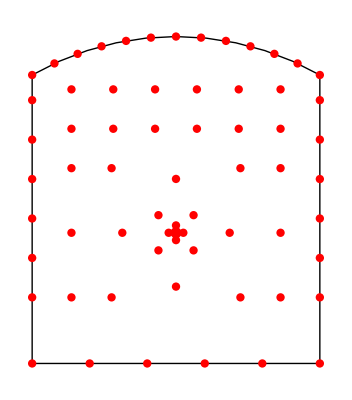

-Graphics3D-

```mathematica
(*Coordenadas dos furos de pilão*)
TBFP1Qx = Table[{i,(A4/2)+BL},{i,((L-(A1 Sqrt[2]))/2),((L+(A1 Sqrt[2]))/2), (A1 Sqrt[2])/2}];
TBFP1Qy = Table[{L/2,i},{i,((A4- (A1 Sqrt[2]))/2)+BL ,((A4+(A1 Sqrt[2]))/2)+BL ,A1 Sqrt[2]}];
TBFP2Qx = Table[{i,((A4-A2)/2)+BL},{i,((L-A2)/2),((L+A2)/2),A2}];
TBFP2Qy = Table[{i,((A4+A2)/2)+BL},{i,((L-A2)/2),((L+A2)/2),A2}];
TBFP3Qx = Table[{i,(A4/2)+BL },{i,((L- (A3 Sqrt[2]))/2),((L+ (A3 Sqrt[2]))/2), A3 Sqrt[2] }];
TBFP3Qy = Table[{L/2,i},{i,((A4- (A3 Sqrt[2]))/2)+BL ,((A4+(A3 Sqrt[2]))/2)+BL ,A3 Sqrt[2]}];
TBFP4Qx = Table[{i,BL},{i,((L-A4)/2),((L+A4)/2),A4}];
TBFP4Qy = Table[{i,BL+A4},{i,((L-A4)/2),((L+A4)/2),A4}];
FuroPilao={L/2,(A4/2)+BL};

(*Coordenadas dos furos de levante*)
TBFLEV = Table[{i, 0},{i,0,L,SL}];

(*Coordenadas dos furos de contorno*)
Hca = Hp + Harc - RaioCirc;
θ = ArcSin[L/(2RaioCirc)];
TBFCT = Table[{(RaioCirc  Cos[α])+L/2,(RaioCirc  Sin[α])+Hca},{α,π/2-θ,π/2+θ, SCT/RaioCirc}];
TBFCP1 = Table[{0,i},{i,BL,Hp-BCT,SCP}];
TBFCP2 = Table[{L,i},{i,BL,Hp-BCT,SCP}];

(*Coordenadas dos furos de expansão*)
If[NLH ≠0,
j = A4+BL+BES;
TBFES={};
While[j≤Hp,
If[j != A4+BL+BES,TBFES=Join[TBFES,Table[{i,j},{i,BCP,L-BCP,SES}]],TBFES= Table[{i,j},{i,BCP,L-BCP,SES}]];
j=j+BES;
],
TBFES={}]
If[NLV!=0,
k=BCP;
TBFEL1={};
While[k<=(((L-A4)/2)-BEL),
If[k≠BCP,TBFEL1=Join[TBFEL1,Table[{k,l},{l,BL,BL+A4,SEL}]],TBFEL1=Table[{k,l},{l,BL,BL+A4,SEL}]] ;
k=k+BEL;
],
TBFEL1={}]

If[NLV!=0,
m=L-BCP;
TBFEL2={};
While[m>=((L+A4)/2+BEL),
If[m≠L-BCP,TBFEL2=Join[TBFEL2,Table[{m,n},{n,BL,BL+A4,SEL}]],TBFEL2=Table[{m,n},{n,BL,BL+A4,SEL}]] ;
m=m-BEL;
],
TBFEL2={}]

(*Coordenadas finais e Gráficos*)
Tabelafuros = Join[TBFP1Qx,TBFP1Qy,TBFP2Qx,TBFP2Qy ,TBFP3Qx,TBFP3Qy,TBFP4Qx,TBFP4Qy, TBFLEV, TBFCT,TBFCP1,TBFCP2,TBFES,TBFEL1,TBFEL2];
Furos2d=Graphics[ListPlot[Tabelafuros,AspectRatio->Automatic,Axes->False,PlotStyle->{PointSize[0.015],Red}]];
FuroVazio=Graphics[{PointSize[0.02],Red,Point[FuroPilao],PointSize[0.025],Red}];
Tunel=Graphics[{EdgeForm[Thin],Line[{{0,Hp},{0,0},{L,0},{L,Hp}}]}];
Arco2d=Graphics[{EdgeForm[{Thin,Black}],Line[Table[{RaioCirc Cos[α]+L/2,RaioCirc Sin[α]+Hca},{α,π/2-θ,π/2+θ,(2θ)/10}]]}];
NCoord =Length[Tabelafuros];
div=H/100;
Tabelafuros3d={};
z=Table[0,NCoord];
cont1=0;
cont2=1;
While[cont2≤100,Tabelafuros3d=Join[Tabelafuros3d,Table[Prepend[Tabelafuros[[i]],z[[i]]],{i,NCoord}]];
cont1=cont1+div;
z =Table[-(cont2 div),NCoord];
cont2++;
]
Furos3d=ListPointPlot3D[Tabelafuros3d,Axes->False,PlotStyle->{PointSize[0.015],Red}];
Prof=5;
Arco3d=ParametricPlot3D[{x,RaioCirc Cos[α]+L/2,RaioCirc Sin[α]+Hca},{α,π/2-θ,π/2+θ},{x,-Prof,0},PlotStyle->Opacity[0.2],Mesh->None];
f1=Graphics3D[{Opacity[0.2],EdgeForm[],Polygon[{{0,0,0},{0,L,0},{-Prof,L,0},{-Prof,0,0}}]}];
f2=Graphics3D[{Opacity[0.2],EdgeForm[],Polygon[{{0,0,0},{0,0,Hp},{-Prof,0,Hp},{-Prof,0,0}}]}];
f3=Graphics3D[{Opacity[0.2],EdgeForm[],Polygon[{{0,L,0},{0,L,Hp},{-Prof,L,Hp},{-Prof,L,0}}]}];
f4a=Graphics3D[{Opacity[0.7],EdgeForm[],Polygon[{{0,0,0},{0,L,0},{0,L,Hp},{0,0,Hp}}]}];
f4b=Graphics3D[{Opacity[0.7],EdgeForm[],Polygon[Table[{0,RaioCirc Cos[α]+L/2,RaioCirc Sin[α]+Hca},{α,π/2-θ,π/2+θ,(2θ)/10}]]}];
Show[Tunel,Arco2d,Furos2d,FuroVazio]
Show[{f1,f2,f3,f4a,f4b,Arco3d,Furos3d},Boxed->False,Axes-> True]
```